#### Разбор вопроса

Пусть у нас есть функция, которая производит громоздкие вычисления и возвращает некоторый список. В целях демонстрации рассмотрим функцию возвращающую степени x

```mathematica
f[x_]:={x, x^2,x^3}
```

И нам необходимо написать функцию, которая каким-то образом работает с элементами этого списка. В целях демонстрации пусть это будет сумма первого и третьего элементов списка, возвращаемого функцией f[x], т.е. x+x^3.
1) Первый способ -- самый наивный:

```mathematica
g[x_]:=f[x]⟦1⟧ + f[x]⟦3⟧
g[x]
```

x+x^3

Недостаток -- функция вызывается дважды. Если бы функция f была по настоящему трудоёмкой, то вы бы ждали вдвое дольше.
2) Второй способ -- добавить вспомогательную функцию, которая делает с элементами списка то, что вы хотите, а итоговую функцию  представить в виде композиции:

```mathematica
tmp[y_]:=y⟦1⟧ + y⟦3⟧
g[x_]:=tmp[f[x]]
g[x]
```

x+x^3

Недостаток --- необходимость вводить вспомогательную функцию и давать ей отдельное имя.
3) Третий способ --- усовершенствование второго. Замена обычной функции на анонимную

```mathematica
g[x_]:=(#⟦1⟧ + #⟦3⟧)&@f[x]
g[x]
```

x+x^3

Выражение (#⟦1⟧ + #⟦3⟧)& объявляет анонимную функцию.
4) Использовать программный модуль Module, который позволяет заводить локальные переменные.

```mathematica
g[x_]:= Module[{y},y=f[x];y⟦1⟧+y⟦3⟧]
g[x]
```

x+x^3

5) Избежать введения дополнительных функций, используя какую-нибудь математическую хитрость

```mathematica
g[x_]:={1,0,1}.f[x]
g[x]
```

x+x^3

## Линейная алгебра

## Векторы

#### Векторы представляются в виде списка чисел.

```mathematica
x={a, b,c};
y={π,ⅇ,√2};
```

#### Все арифметические операторы и ряд функций работают со списками поэлементно. Например, можно складывать, вычитать векторы одинакового размера или вектор и скаляр.

```mathematica
x+y
```

{a+π,b+ⅇ,√2+c}

```mathematica
x-y
```

{a-π,b-ⅇ,-√2+c}

```mathematica
x+π
```

{a+π,b+π,c+π}

#### Все это распространяется и на оператор умножения *, оператор деления / и оператор возведение в степень. Все операции выполняются поэлементно

```mathematica
x*y
```

{a π,b ⅇ,√2 c}

```mathematica
x/y
```

{a/π,b/ⅇ,c/(√2)}

```mathematica
x^y
```

{a^π,b^ⅇ,c^(√2)}

#### За скалярное произведение отвечает функция Dot и оператор точка “.”

```mathematica
Dot[x,y]
```

√2 c+b ⅇ+a π

```mathematica
x.y
```

√2 c+b ⅇ+a π

#### За векторное произведение отвечает функция Cross и оператор “×” (escape + cross + escape)

```mathematica
Cross[x,y]
```

{√2 b-c ⅇ,-√2 a+c π,a ⅇ-b π}

```mathematica
x ×y
```

{√2 b-c ⅇ,-√2 a+c π,a ⅇ-b π}

#### Внешнее произведение можно вычислить функцией KroneckerProduct

```mathematica
KroneckerProduct[x, y]//MatrixForm
```

(a π | a ⅇ | √2 a
b π | b ⅇ | √2 b
c π | c ⅇ | √2 c)

## Матрицы

#### Матрицы задаются, как список строк

```mathematica
A = {{Cos[ϕ], Sin[ϕ]},{-Sin[ϕ], Cos[ϕ]}};
```

#### IdentityMatrix --- единичная матрица

```mathematica
B=π IdentityMatrix[2];
B
```

{{π,0},{0,π}}

#### Вывести список списков в матричном виде можно используя MatrixForm

```mathematica
A//MatrixForm
```

(Cos[ϕ] | Sin[ϕ]
-Sin[ϕ] | Cos[ϕ])

#### Все основные арифметические операторы работают с матрицами также, как и с векторами

```mathematica
A*B//MatrixForm
```

(π Cos[ϕ] | 0
0 | π Cos[ϕ])

#### Матричное умножение --- оператор точка или функция Dot

```mathematica
A.B //MatrixForm
```

(π Cos[ϕ] | π Sin[ϕ]
-π Sin[ϕ] | π Cos[ϕ])

#### Определитель матрицы --- функция Det

```mathematica
Det[A]//Simplify
```

1

#### Ранг матрицы --- MatrixRank

```mathematica
MatrixRank[A]
```

2

#### RowReduce приводит матрицу к ступенчатому виду

```mathematica
RowReduce[{{1,2,3},{4,5,6},{7,8,9}}]//MatrixForm
```

(1 | 0 | -1
0 | 1 | 2
0 | 0 | 0)

#### NullSpace --- нулевое пространство оператора

```mathematica
A={{1,2,3},{2,3,5}};
nullspace=NullSpace[A]
```

{{-1,-1,1}}

```mathematica
A.nullspace⟦1⟧
```

{0,0}

#### Транспонированная матрица --- Transpose

```mathematica
Transpose[A]//MatrixForm
```

(Cos[ϕ] | -Sin[ϕ]
Sin[ϕ] | Cos[ϕ])

#### Или можно сокращенно записать Aᵀ (escape+ tr+escape)

```mathematica
Aᵀ//MatrixForm
```

(Cos[ϕ] | -Sin[ϕ]
Sin[ϕ] | Cos[ϕ])

#### Обратная матрица --- Inverse

```mathematica
inversedA= Inverse[A];
inversedA//Simplify//MatrixForm
```

(Cos[ϕ] | -Sin[ϕ]
Sin[ϕ] | Cos[ϕ])

```mathematica
inversedA.A//Simplify
```

{{1,0},{0,1}}

#### Собственные числа можно найти функцией Eigenvalues

```mathematica
Eigenvalues[A]
```

{Cos[ϕ]-ⅈ Sin[ϕ],Cos[ϕ]+ⅈ Sin[ϕ]}

#### Собственные вектор --- функцией Eigenvectors

```mathematica
Eigenvectors[A]
```

{{ⅈ,1},{-ⅈ,1}}

#### Функцией Eigensystem можно найти сразу и то и другое

```mathematica
Clear[x]
{λ,x} =Eigensystem[A];
A.x⟦1⟧==λ⟦1⟧x⟦1⟧//Simplify
A.x⟦2⟧==λ⟦2⟧x⟦2⟧//Simplify
```

True

True

#### Сингулярные значения и векторы можно найти Функцией SingularValueDecomposition

```mathematica
A={{1, 2},{3,4},{5,6}};
A//MatrixForm
```

(1 | 2
3 | 4
5 | 6)

```mathematica
{u,w,v}=SingularValueDecomposition[A];
u.w.Transpose[v]==A//FullSimplify
```

True

#### Псевдообращение матрицы функцией PseudoInverse

```mathematica
B=PseudoInverse[A];
B//MatrixForm
```

(-4/3 | -1/3 | 2/3
13/12 | 1/3 | -5/12)

```mathematica
MatrixPlot[{{-4/3,-1/3,2/3},{13/12,1/3,-5/12}}]
```

```mathematica
B. A
```

{{1,0},{0,1}}

## Системы линейных уравнения

#### LinearSolve решает системы линейных уравнений. Принимает матрицу левой части и правую часть.

```mathematica
A={{1,2},{3,4}};
b={1,-1};
x=LinearSolve[A,b]
```

{-3,2}

```mathematica
A.x==b
```

True

```mathematica
x==Inverse[A].b
```

True

## Нелинейные уравнения

## Задание уравнений

### Уравнения задаются с помощью оператора сравнения ==.

```mathematica
x+1==1
```

### Если выражения слева и справа заведомо равны, то вы сразу и получите True

```mathematica
2+2==4
```

```mathematica
2+2==5
```

### Можно запоминать уравнение в переменную

```mathematica
eq = x+1==1
```

### Есть три способа задать систему уравнений

Задать список уравнений

```mathematica
eq={x+y==1, x-y==1}
```

Задать список левых частей и  правых частей и поставить между ними оператор ==

```mathematica
eq ={x+y, x-y}=={1, 1}
```

Использовать логический оператор &&

```mathematica
eq = (x+y == 1)&&(x-y==1)
```

## Корни функции одной переменной

### Функция FindRoot численно ищет корень в окрестности указанной точки. Возвращает правило в форме x → root Принимает как и уравнение, так и просто функцию.

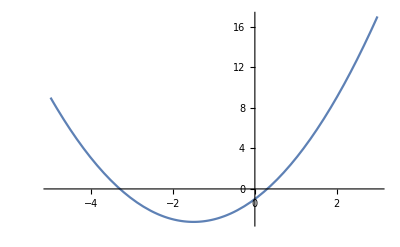

-1+3 x+x^2

```mathematica
f[x_]:=x^2+3x-1
Plot[f[x],{x, -5, 3}]
Factor[f[x]]
```

```mathematica
root=FindRoot[f[x],{x, 0}, PrecisionGoal->10]
```

{x→0.302776}

```mathematica
f[x]/.root
```

2.35922×10^-16

### Функция Solve ищет корни уравнения аналитически.

```mathematica
Solve[f[x]==0,x]
```

{{x→1/2 (-3-√13)},{x→1/2 (-3+√13)}}

### Если корней найти не удаётся, то возвращается пустой список {}

```mathematica
Solve[x+1==x,x]
```

{}

### Если корней бесконечно много, то возвращается список списков {{}}

```mathematica
Solve[x==x,x]
```

{{}}

### Принимает область определения неизвестной третьим аргументом

```mathematica
Solve[x^4==1,x]
```

{{x→-1},{x→-ⅈ},{x→ⅈ},{x→1}}

```mathematica
Solve[x^4==1, x,Reals]
```

{{x→-1},{x→1}}

### Задать ограничения вида неравенство можно логическим оператором && или задав список условий

```mathematica
Solve[x^4==1&&x>0,x, Reals]
```

{{x→1}}

```mathematica
Solve[{x^4==1,x>0},x, Reals]
```

{{x→1}}

### Если система не может найти корень, то она не производит изменений и выводит сообщение об ошибке

```mathematica
Solve[Cos[x]+Exp[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^x+Cos[x]==0,x]

### Если система знает, что корень найти можно, но он не выражается аналитически, то она просто запомнит, что результат действия этой операции --- это список корней уравнения.

```mathematica
Solve[x^5-x+1==0,x]
```

{{x→Root[1-#1+#1^5&,1]},{x→Root[1-#1+#1^5&,2]},{x→Root[1-#1+#1^5&,3]},{x→Root[1-#1+#1^5&,4]},{x→Root[1-#1+#1^5&,5]}}

### NSolve --- численный аналог для функции Solve

```mathematica
NSolve[x^5-x+1==0,x]
```

{{x→-1.1673},{x→-0.181232-1.08395 ⅈ},{x→-0.181232+1.08395 ⅈ},{x→0.764884-0.352472 ⅈ},{x→0.764884+0.352472 ⅈ}}

```mathematica
NSolve[x^5-x+1==0,x,Reals]
```

{{x→-1.1673}}

```mathematica
NSolve[x^5-x+1==0,x,Reals,10]
```

{{x→-1.167303978}}

### Функция Reduce тоже может использована для решений уравнений, но она даёт свои ответы в другой форме.

```mathematica
roots=Reduce[x^5-x+1==0,x]
```

x==Root[1-#1+#1^5&,1]||x==Root[1-#1+#1^5&,2]||x==Root[1-#1+#1^5&,3]||x==Root[1-#1+#1^5&,4]||x==Root[1-#1+#1^5&,5]

### Функция ToRules позволяет получить из этого ответ в форме подстановки

```mathematica
roots=ToRules[roots]
```

Sequence[{x→Root[1-#1+#1^5&,1]},{x→Root[1-#1+#1^5&,2]},{x→Root[1-#1+#1^5&,3]},{x→Root[1-#1+#1^5&,4]},{x→Root[1-#1+#1^5&,5]}]

```mathematica
x^5-x+1/.{roots}//Simplify
```

{0,0,0,0,0}

## Оптимизации

#### Для решения задач минимизации тоже существует ряд методов

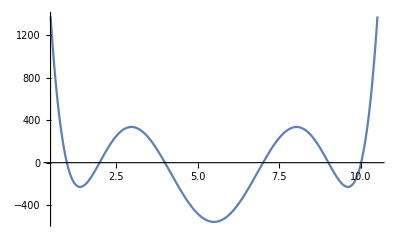

```mathematica
f[x_]:=Expand[(x-1)(x-2)(x-4)(x-7)(x-9)(x-10)];
pic1=Plot[f[x],{x,0.5,10.5}]
```

#### Функция ArgMin ищет точку минимума

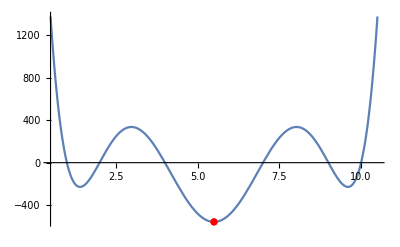

```mathematica
x0=ArgMin[f[x],x];
y0=f[x0];
Show[pic1, ListPlot[{{Subscript[x, 0], Subscript[y, 0]}}, PlotStyle->Red]]
```

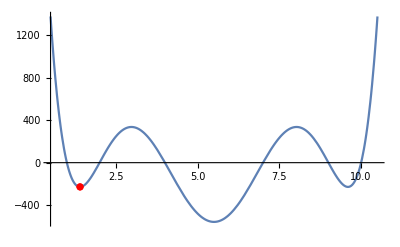

```mathematica
x1=ArgMin[{f[x],x≤3},x];
y1=f[x1];
Show[pic1, ListPlot[{{x1, y1}}, PlotStyle->Red]]
```

#### Функция MinValue ищет минимальное значение функции

```mathematica
y2=MinValue[f[x],x];
y2==y0
```

True

#### Функция Minimize ищет и то, и то

```mathematica
Minimize[f[x],x]
```

{-35721/64,{x→11/2}}

#### NMinimize численно ищет минимум

```mathematica
NMinimize[f[x],x]
```

{-228.4,{x→1.40242}}

#### FindMinimum численно ищет минимум в окрестности точки

```mathematica
min=FindMinimum[f[x],{x,0}]
x3=x/.min⟦2⟧;
y3=min⟦1⟧;
Show[pic1, ListPlot[{{x3, y3}}, PlotStyle->Red]]
```

{-228.4,{x→1.40242}}

-Graphics-

#### Все эти функции работают и для многомерных случаев

```mathematica
f[x_,y_]:=x+y
restrictions[x_,y_]:=x^2+y^2≤1
min=Minimize[{f[x,y],restrictions[x,y]},{x,y}]
```

{-√2,{x→-1/(√2),y→-1/(√2)}}

```mathematica
zmin=min⟦1⟧;
{xmin,ymin}={x,y}/.min⟦2⟧;
pic1=Plot3D[f[x,y],{x,y}∈Disk[]];
pic2=ListPointPlot3D[{{xmin,ymin,zmin}},PlotStyle->Red];
Show[pic1,pic2]
```

-Graphics3D-

# Решение дифференциальных уравнений

#### Способы задать дифференциальное уравнение: 1) Используя штрих ‘

```mathematica
y'[x]==y[x]
```

y'[x]==y[x]

#### 2) Используя функцию D[]

```mathematica
D[y[x],x]==y[x]
```

y'[x]==y[x]

#### 3) Используя ∂_x

```mathematica
D[y[x], x]==y[x]
```

y'[x]==y[x]

```mathematica
DSolve[eq,y,x]
```

{{y→Function[{x},ⅇ^x C[1]]}}

#### Функция DSolve решает дифференциальные уравнения

```mathematica
eq=y'[x]==1
sol=DSolve[eq,y[x],x]
```

y'[x]==1

{{y[x]→x+C[1]}}

```mathematica
f[x_]:=y[x]/.sol⟦1⟧
f[x]
```

x+C[1]

#### Начальные условия можно указать рядом с уравнением

```mathematica
initial=y[0]==0
sol=DSolve[{eq,initial},y[x],x]
```

y[0]==0

{{y[x]→x}}

#### NDSolve численно решает дифференциальные уравнения численно

```mathematica
eq=y'[x]+y[x]^2==Sin[x]
DSolve[{eq,initial},y[x],x]
```

y[x]^2+y'[x]==Sin[x]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[{y[x]^2+y'[x]==Sin[x],y[0]==0},y[x],x]

```mathematica
sol=NDSolve[{eq,initial},y[x],{x,0,5}]
```

{{y[x]→InterpolatingFunction[…][x]}}

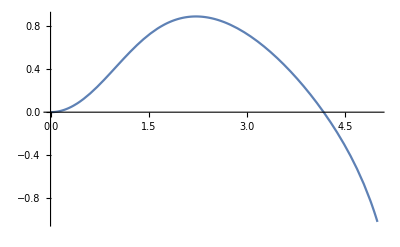

```mathematica
Plot[y[x]/.sol,{x,0,5}]
```